```mathematica
Clear["Global`*"]
```

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

ListLinePlot::lpn: Flatten[$Failed] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[Flatten[$Failed],PlotRange→All,PlotLabel→nAtom]

-Graphics-

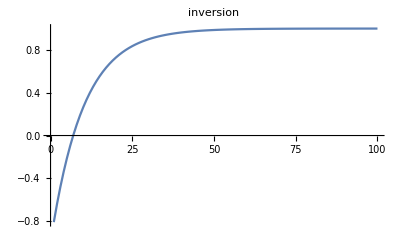

-Graphics-

```mathematica
(*When doing one run*)
name ="N100_repumping0p5";
intensityy=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
inversionn=Flatten[Import[NotebookDirectory[]<>name<>"/inversion.dat"]];
spinSpinCorr=Flatten[Import[NotebookDirectory[]<>name<>"/spinSpinCor.dat"]];
ListLinePlot[intensityy,PlotRange->All,PlotLabel->intensity]
ListLinePlot[inversionn,PlotRange->All,PlotLabel->inversion]
ListLinePlot[spinSpinCorr,PlotRange->All,PlotLabel->spinSpinCor]
```

```mathematica
(*When using bash*)
```

```mathematica
L=Table[0,{i,20}];
```

```mathematica
For[i=0,i<20,i++,
x=Flatten[Import[NotebookDirectory[]<>"meanP"<>ToString[i]<>"/nAtom.dat"]];
x=Cases[x,Except[0|0.]];
L[[i+1]]=Last[x];
]
```

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

```mathematica
nAtomSS=Flatten[Import["/Users/westgatesnow/Desktop/Codes/2017/beamLaser/versusTau/nAtomSS.dat"]];
```

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

```mathematica
nAtomSS
```

Flatten[$Failed]

```mathematica
L
```

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
ListLinePlot[L]
```

-Graphics-